```mathematica
NodeTypes={"Input","Hidden","Output","Bias"};
ActivationFunction ={"Sine","Abs","Id","Mod","Gaus"};
```

```mathematica
GetPathFromNo[orgNo_]:= StringForm["D:\\betterOutput\\organisms\\org``.json",orgNo]//ToString;
GetOrganism[path_]:=
Quiet[
{
"genome",
"nervesystem",
"parent"
}/.Import[path]
]
{g,n,p}=GetOrganism[GetPathFromNo[0]];
DrawGenome[path_]:=Module[{g,n,p,vertices,vertexInfo,vertexStyle,edges,weights},
{g,n,p}=GetOrganism[path];
vertices="i"/.("vertices"/.g);
vertexInfo="i"->Tooltip["i",StringForm["i: ``\ntype: ``\nf: ``.","i",NodeTypes⟦"type"+1⟧//Quiet,ActivationFunction⟦"f"+1⟧//Quiet]]/.("vertices"/.g);
vertexStyle=("i"->{"type"}/.("vertices"/.g))/.{{0}->RGBColor[0.368627, 0.556863, 0.956863],{1}->RGBColor[0.72, 0.72, 0.72],{2}->RGBColor[0.72, 0.28, 0.32],{3}->RGBColor[0.92, 0.67, 0.32]};
Print[vertexStyle];
edges = "i"->"o"/.("links"/.g);
weights=("w"/.("links"/.g));
Graph[
vertices,
edges,
EdgeWeight->weights,
VertexLabels->vertexInfo,
VertexStyle->vertexStyle,
GraphLayout->"LayeredEmbedding"
(*,EdgeLabels->"EdgeWeight"*)
]
]
DrawNerveSystem[path_]:=Module[{g,n,p,vertices,vertexTypes,edges,weights,vertexStyle},
{g,n,p}=GetOrganism[path];
vertices="i"/.("vertices"/.n);
vertexTypes="i"->Tooltip["i",StringForm["i: ``\ntype: ``","i","type"]]/.("vertices"/.n);
vertexStyle=("i"->{"type"}/.("vertices"/.g))/.{{0}->RGBColor[0.368627, 0.556863, 0.956863],{1}->RGBColor[0.72, 0.72, 0.72],{2}->RGBColor[0.72, 0.28, 0.32]};
edges = "i"->"o"/.("links"/.n);
weights=("w"/.("links"/.n));
Graph[
vertices,
edges,
EdgeWeight->weights,
VertexLabels->vertexTypes,
VertexStyle->vertexStyle
(*,EdgeLabels->"EdgeWeight"*)
]
]
```

Set::shape: Lists {g,n,p} and {genome,nervesystem,parent}/.$Failed are not the same shape.

```mathematica
dir=SystemDialogInput["FileOpen"]
```

D:\betterEnergy\initOrg.json

{0→RGBColor[0.368627, 0.556863, 0.956863],1→RGBColor[0.368627, 0.556863, 0.956863],2→RGBColor[0.368627, 0.556863, 0.956863],3→RGBColor[0.368627, 0.556863, 0.956863],4→RGBColor[0.72, 0.28, 0.32],5→RGBColor[0.72, 0.28, 0.32],6→RGBColor[0.72, 0.28, 0.32],7→RGBColor[0.72, 0.28, 0.32],8→RGBColor[0.72, 0.28, 0.32],9→RGBColor[0.72, 0.28, 0.32],10→RGBColor[0.72, 0.28, 0.32],11→RGBColor[0.72, 0.28, 0.32],12→RGBColor[0.72, 0.28, 0.32],13→RGBColor[0.72, 0.28, 0.32],14→RGBColor[0.72, 0.28, 0.32],15→RGBColor[0.92, 0.67, 0.32]}

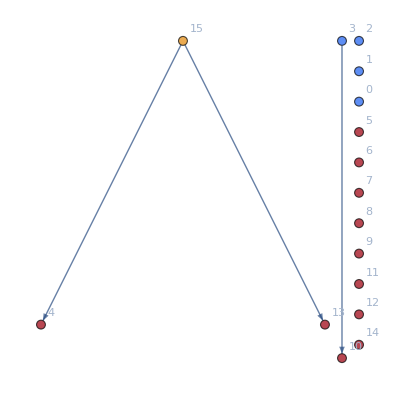

```mathematica
g=DrawGenome[dir]
```

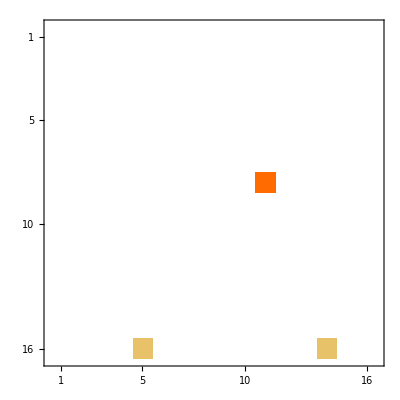

```mathematica
MatrixPlot[WeightedAdjacencyMatrix[g]]
```

```mathematica
n=DrawNerveSystem[GetPathFromNo[91678]]
(*WeightedAdjacencyMatrix[n]//MatrixPlot*)
```

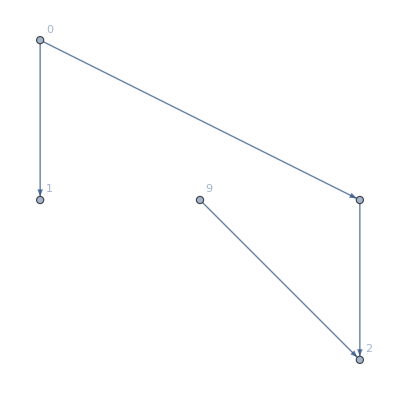

```mathematica
Graph[{0,1,2,9},{9->2,0->1,0->10,10->2},EdgeWeight->{-0.643733,1.464747,1.,0.83928},VertexLabels->{0->0,1->1,2->2,9->9}]
```

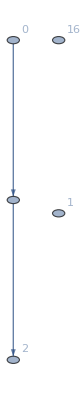

```mathematica
Graph[{0,1,2,16},{0->17,17->2},EdgeWeight->{1.,0.374369},VertexLabels->{0->0,1->1,2->2,16->16}]
```

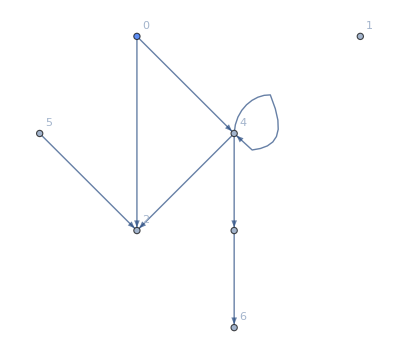

```mathematica
Graph[{0,1,2,4,5,6},{0->2,0->4,5->2,4->4,4->2,4->7,7->6},EdgeWeight->{0.83928,1.,-0.012649,-0.841888,0.257623,1.,1.},VertexLabels->{0->0,1->1,2->2,4->4,5->5,6->6},VertexStyle->{0->RGBColor[0.368627, 0.556863, 0.956863]}]
```